```mathematica
f[x_,y_] := (3-y)*y
```

```mathematica
EulersMethod[x0_,y0_,h_,halt_]:=Module[{x=x0,y=y0,j,points={{x0,y0}}},For[j=1,j≤halt,j++,y=y+h*f[x,y];
x=x+h;
points=Append[points,{x,y}]];
Return[points]];
```

```mathematica
solapprox=EulersMethod[0, 2,0.1, 20]
```

{{0,2},{0.1,2.2},{0.2,2.376},{0.3,2.52426},{0.4,2.64435},{0.5,2.7384},{0.6,2.81003},{0.7,2.86342},{0.8,2.90253},{0.9,2.93082},{1.,2.95109},{1.1,2.96553},{1.2,2.97575},{1.3,2.98297},{1.4,2.98805},{1.5,2.99162},{1.6,2.99413},{1.7,2.99588},{1.8,2.99712},{1.9,2.99798},{2.,2.99859}}

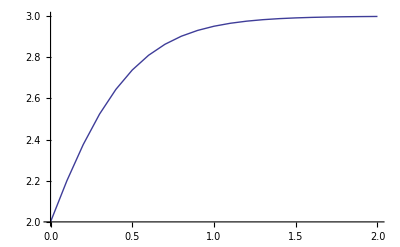

```mathematica
Papprox=ListPlot[solapprox, Joined -> True, PlotStyle -> Thick]
```

```mathematica
sol := NDSolve[{y'[x] == y[x](3-y[x]), y[0] == 2}, y, {x,0,2}]
```

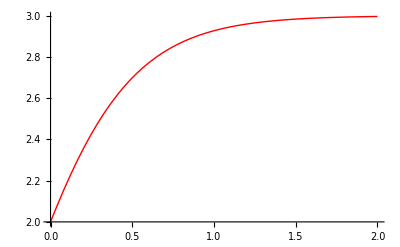

```mathematica
Ptrue = Plot[Evaluate[y[x] /. sol], {x,0,2}, PlotStyle -> {Thick,Red}]
```

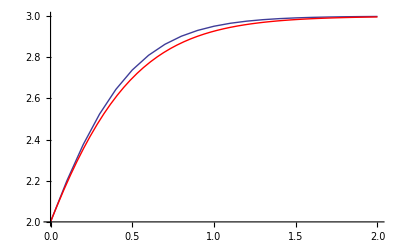

```mathematica
Show[Papprox, Ptrue]
```